# RG Scheme for 1- and 2-Point Functions:

## 1) Making the Coupling Vector A[i]=(K[i];p):

Here, we must declare all variables as additional couplings:

```mathematica
Clear[A,B,μ,η]
dim=5;
A[3]=B[3]=μ;
A[4]=B[4]=η;
Clear[x0,x1,x2]
Z0[x0_,x1_,x2_]:=Exp[-A[0]]*
A[1]^(-((x0+x1)+(x1+x2))/4)*
A[2]^(-(x0*x1+x1*x2)/4)*μ^(-(x0*x2)/4)
Z1[x0_,x2_]:=Exp[-B[0]/2]*
B[1]^(-(x0+x2)/4)*
B[2]^(-(x0*x2)/4)
TrZ0[x0_,x2_]:=Sum[Z0[x0,x1,x2],{x1,-1,1,2}]
i=0;
For[x0=-1,x0≤1,x0+=2,
For[x2=-1,x2≤1,x2+=2,
leq[i]=Z1[x0,x2];
req[i++]=TrZ0[x0,x2];
]
]
leq[0]==req[0];
leq[1]==req[1];
leq[2]==req[2];
leq[3]==req[3];
SB[0]=Simplify[Solve[leq[0]*leq[1]*leq[2]*leq[3]==req[0]*req[1]*req[2]*req[3],B[0]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&C[1]==0][[1]]
SB[1]=Factor[Simplify[Solve[Factor[leq[0]/leq[3]]==Factor[req[0]/req[3]],B[1]]]][[1]]
SB[2]=Factor[Simplify[Solve[Factor[(leq[3]*leq[0])/(leq[1]*leq[2])]==Factor[(req[3]*req[0])/(req[1]*req[2])],B[2]]]][[1]]

SBT=Table[Part[SB[n],1],{n,0,2}];
Print["Raw Coupling:"]
SIC={B[0]->0,B[1]->η,B[2]->μ}
```

{B[0]→1/2 Log[(ⅇ^(4 A[0]) A[1]^2 A[2])/((1+A[1])^2 (A[2]+A[1]^2 A[2]+A[1] (1+A[2]^2)))]}

{B[1]→(A[1] (A[1]+A[2]))/(1+A[1] A[2])}

{B[2]→(μ (1+A[1])^2 A[2])/((A[1]+A[2]) (1+A[1] A[2]))}

Raw Coupling:

{B[0]→0,B[1]→η,B[2]→μ}

## 3) Comparing the RG-Flow with the Partition Function:

Operators to initiate and increment the RG-Flow:

```mathematica
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}]
RG:=SAT=Table[A[n]->B[n]/.FullSimplify[SBT/.SAT,Assumptions->μ>0&&η>0],{n,0,dim-1}]
(*Final,three-spin Partition Function with renormalized couplings:*)
LnZ1=Log[Sum[Sum[Sum[
Exp[-A[0]]*
A[1]^(-((x0+x1)+(x1+x2))/4)*
A[2]^(-(x0*x1+x1*x2)/4)*
A[3]^(-(x0*x2)/4)*
A[4]^(-(x0+x2)/4),
{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+Simplify[(LnZ1/.A[0]->0),Assumptions->η>0]
DLnZ1=Factor[Simplify[Table[D[LnZ1,A[i]],{i,0,dim-1}],Assumptions->μ>0&&η>0&&A[1]>0&&A[2]>0]];
(*Makes any raw Partition Function Z_k,here only used to test RG-flow:*)
θ[k_,x_,y_,z_]:=Block[{a,b},
If[k==0,
Return[η^(-(x+y+z)/2)*μ^(-(x*y+y*z+x*z)/4)],
Return[Expand[μ^(-(x*z)/4)*η^(y/2)*Sum[Sum[θ[k-1,x,a,y]*θ[k-1,y,b,z],{a,-1,1,2}],{b,-1,1,2}]]]
]
]
Z[k_]:=If[k>0,Return[Sum[Sum[Sum[θ[k-1,x,y,z],{x,-1,1,2}],{y,-1,1,2}],{z,-1,1,2}]],Return[1]]
```

-A[0]+Log[(1+2 √(η μ) √A[1] √A[2]+2 √(η μ) A[1]^(3/2) √A[2]+A[1] A[2]+η A[1] (A[1]+A[2]))/(μ^(1/4) A[1] √(η A[2]))]

```mathematica
InitRG
Factor[FullSimplify[Exp[LnZ1]/.SAT,Assumptions->μ>0&&η>0]]
Factor[Z[1]];
Factor[%%/%]
```

{A[0]→0,A[1]→η,A[2]→μ,μ→μ,η→η}

((1+η) (1-η+η^2+3 η μ))/(η^(3/2) μ^(3/4))

1

Here is a test for Z_2:

```mathematica
InitRG;RG;
Factor[FullSimplify[Exp[LnZ1]/.SAT,Assumptions->μ>0&&η>0]];
Factor[Z[2]]
Factor[%%/%]
```

((1+η) (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2)))/(η^(5/2) μ^(7/4))

1

Here is a test for Z_3:

```mathematica
InitRG;RG;RG;
Factor[FullSimplify[Exp[LnZ1]/.SAT,Assumptions->μ>0&&η>0]]
Factor[Z[3]];
Factor[%%/%]
```

1/(η^(9/2) μ^(15/4))(1+η) (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5)

1

## 4) Calculating One-Point Functions:

Defining the full W-matrix (also called the Jacobian):

```mathematica
Clear[η,μ]
MatrixForm[W=Factor[Table[D[(B[j]/.SBT),A[i]],{i,0,dim-1},{j,0,dim-1}]]]
(*Operators to initiate and increment the RG-Flow of Υ with the W-Matrix:*)
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
```

(2 | 0 | 0 | 0 | 0
-((-1+A[1]) (A[1]+2 A[2]+2 A[1] A[2]+2 A[1]^2 A[2]+A[1] A[2]^2))/(2 A[1] (1+A[1]) (A[1]+A[2]) (1+A[1] A[2])) | (2 A[1]+A[2]+A[1]^2 A[2])/(1+A[1] A[2])^2 | (μ (-1+A[1]) (1+A[1]) (-1+A[2])^2 A[2])/((A[1]+A[2])^2 (1+A[1] A[2])^2) | 0 | 0
-(A[1] (-1+A[2]) (1+A[2]))/(2 A[2] (A[1]+A[2]) (1+A[1] A[2])) | -((-1+A[1]) A[1] (1+A[1]))/(1+A[1] A[2])^2 | -(μ A[1] (1+A[1])^2 (-1+A[2]) (1+A[2]))/((A[1]+A[2])^2 (1+A[1] A[2])^2) | 0 | 0
0 | 0 | ((1+A[1])^2 A[2])/((A[1]+A[2]) (1+A[1] A[2])) | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
InitRGW
Υ
RGW;
Υ
(*First derivative of the elementary PF:*)
DLnZ1=Factor[Simplify[Table[D[LnZ1,A[i]],{i,0,dim-1}],Assumptions->μ>0&&η>0&&A[1]>0&&A[2]>0]]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

{{2,0,0,0,0},{-((-1+η) (η+2 μ+2 η μ+2 η^2 μ+η μ^2))/(2 η (1+η) (η+μ) (1+η μ)),(2 η+μ+η^2 μ)/(1+η μ)^2,((-1+η) (1+η) (-1+μ)^2 μ^2)/((η+μ)^2 (1+η μ)^2),0,0},{-(η (-1+μ) (1+μ))/(2 μ (η+μ) (1+η μ)),-((-1+η) η (1+η))/(1+η μ)^2,-(η (1+η)^2 (-1+μ) μ (1+μ))/((η+μ)^2 (1+η μ)^2),0,0},{0,0,((1+η)^2 μ)/((η+μ) (1+η μ)),1,0},{0,0,0,0,1}}

{-1,(-1+η A[1]^2-√(η μ A[1] A[2])+√(η μ A[1]^3 A[2]))/(A[1] (1+η A[1]^2+A[1] A[2]+η A[1] A[2]+2 √(η μ A[1] A[2])+2 √(η μ A[1]^3 A[2]))),(-1-η A[1]^2+A[1] A[2]+η A[1] A[2])/(2 A[2] (1+η A[1]^2+A[1] A[2]+η A[1] A[2]+2 √(η μ A[1] A[2])+2 √(η μ A[1]^3 A[2]))),-(η (√(η μ)+η √(η μ) A[1]^2+√(η μ) A[1] A[2]+η √(η μ) A[1] A[2]-2 η μ √(A[1] A[2])-2 η μ √(A[1]^3 A[2])))/(4 (η μ)^(3/2) (1+η A[1]^2+A[1] A[2]+η A[1] A[2]+2 √(η μ A[1] A[2])+2 √(η μ A[1]^3 A[2]))),(-1+η A[1]^2-A[1] A[2]+η A[1] A[2])/(2 η (1+η A[1]^2+A[1] A[2]+η A[1] A[2]+2 √(η μ A[1] A[2])+2 √(η μ A[1]^3 A[2])))}

Test of Υ-Flow: First, for the internal energy....

```mathematica
InitRGW
dμdβ=-4μ
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}]
Factor[(dA0dμ.Υ).FullSimplify[(DLnZ1/.SAT),μ>0&&η>0]]
Factor[dμdβ*D[Log[Z[1]],μ]]
Factor[%%/%]
```

-4 μ

{0,0,-4 μ,-4 μ,0}

-(3 (-1+η-η^2+η μ))/(1-η+η^2+3 η μ)

(3 (1-η+η^2-η μ))/(1-η+η^2+3 η μ)

1

...and second for the magnetization:

```mathematica
Clear[μ,η]
InitRGW
dηdH=-2η (**)
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}]
Factor[(dA0dη.Υ).FullSimplify[(DLnZ1/.SAT),μ>0&&η>0]]
Factor[dηdH*D[Log[Z[1]],η]]
Factor[%%/%]
```

-2 η

{0,-2 η,0,0,-2 η}

-(3 (-1+η) (1+η+η^2+η μ))/((1+η) (1-η+η^2+3 η μ))

-(3 (-1+√η) (1+√η) (1+η+η^2+η μ))/((1+η) (1-η+η^2+3 η μ))

1

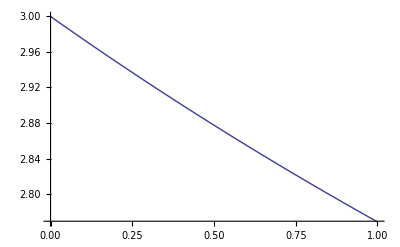

```mathematica
Clear[η,μ]
η=0.04;
Plot[-(3 (-1+η) (1+η+η^2+η μ))/((1+η) (1-η+η^2+3 η μ)),{μ,0,1}]
```

```mathematica
RGW
Factor[(dA0dη.Υ).FullSimplify[(DLnZ1/.SAT),μ>0&&η>0]]
Factor[dηdH*D[Log[Z[2]],η]]
Factor[%%/%]
```

-((-1+η) (5+5 η+5 η^2+5 η^3+5 η^4+6 η μ+6 η^2 μ+6 η^3 μ+6 η μ^(3/2)+8 η^2 μ^(3/2)+6 η^3 μ^(3/2)+3 η μ^2+7 η^2 μ^2+3 η^3 μ^2+4 η^2 μ^(5/2)))/((1+η) (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2)))

-((-1+√η) (1+√η) (5+5 η+5 η^2+5 η^3+5 η^4+6 η μ+6 η^2 μ+6 η^3 μ+6 η μ^(3/2)+8 η^2 μ^(3/2)+6 η^3 μ^(3/2)+3 η μ^2+7 η^2 μ^2+3 η^3 μ^2+4 η^2 μ^(5/2)))/((1+η) (1-η+η^2-η^3+η^4+2 η μ-2 η^2 μ+2 η^3 μ+2 η μ^(3/2)+2 η^3 μ^(3/2)+η μ^2+3 η^2 μ^2+η^3 μ^2+4 η^2 μ^(5/2)))

1

## 5) Calculating Two-Point Functions:

This makes Ω as a Matrix (i,j) of vectors k: (Put k in the middle so that we can dot-product from left and right!)

```mathematica
Clear[η,μ];
Ω=Factor[Table[D[D[(B[j]/.SBT),A[i]],A[k]],{k,0,dim-1},{j,0,dim-1},{i,0,dim-1}]];
InitRGΩ:=Block[{},
InitRGW;
Λ=0*Array[KroneckerDelta,{dim,dim,dim}];
(*Λ=Table[D[Υ,A[j]],{j,0,dim-1}];  This is all zero, anyway! *)
];
RGΩ:=Block[{},
Λ=Together[Together[Λ.Together[W/.SAT]]+Transpose[Together[(Υ.Together[Ω/.SAT]).Transpose[Υ]],{1,3,2}]];
RGW;
];
D2LnZ1=Factor[Table[D[DLnZ1,A[i]],{i,0,dim-1}]];
```

```mathematica
InitRGΩ
Υ;
Λ;
RGΩ;
Υ;
Λ;
```

Test for the specific heat:

```mathematica
Clear[η,μ]
InitRGΩ
dμdβ=-4μ
d2μdβ2=16μ
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}]
d2A0dμ2=D[dA0dμ,μ]
η=1
```

-4 μ

16 μ

{0,0,1,1,0}

{0,0,0,0,0}

1

```mathematica
Clear[η,μ,T]
InitRGΩ
dμdβ=-4μ;
d2μdβ2=16μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
η=1;
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0];
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0];
term0=Factor[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ];
term1=Factor[d2μdβ2*(dA0dμ.Υ).DlnZ];
term2=Factor[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ)];
term3=Factor[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ)];
Factor[dμdβ^2*D[Log[Z[1]],{μ,2}]+d2μdβ2*D[Log[Z[1]],{μ,1}]]
Factor[(term0+term1+term2+term3)/%]
Factor[(dμdβ)^2*D[Log[Z[1]],{μ,2}]/Z[1]]
Factor[D[Factor[dμdβ*D[Log[Z[1]],μ]],μ]*dμdβ]
```

(48 μ)/(1+3 μ)^2

1

-(6 μ^(3/4) (-1-6 μ+3 μ^2))/(1+3 μ)^3

(48 μ)/(1+3 μ)^2

```mathematica
Factor[-1-6 μ+3 μ^2]
```

-1-6 μ+3 μ^2

```mathematica
T=-4/Log[μ];
Z11=Plot[(48 μ)/((16/Log[μ]^2) *(1+3 μ)^2)*1/3,{μ,0,1}];
Z12=Plot[(48 μ)/((-4/Log[μ]) *(1+3 μ)^2)*1/3,{μ,0,1}];
```

```mathematica
RGΩ;
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0];
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0];
term0=Factor[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ];
term1=Factor[d2μdβ2*(dA0dμ.Υ).DlnZ];
term2=Factor[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ)];
term3=Factor[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ)];
Factor[dμdβ^2*D[Log[Z[2]],{μ,2}]+d2μdβ2*D[Log[Z[2]],{μ,1}]]
Factor[(term0+term1+term2+term3)/%]
Factor[D[-D[Log[Z[2]],μ]*dμdβ,μ]]*dμdβ*D[1/T,T]
```

(16 μ (2+9 √μ+20 μ+27 μ^(3/2)+10 μ^2+23 μ^(5/2)+16 μ^3+5 μ^(7/2)))/((1+√μ)^2 (1-√μ+3 μ+μ^(3/2)+4 μ^2)^2)

1

(16 μ (2+9 √μ+20 μ+27 μ^(3/2)+10 μ^2+23 μ^(5/2)+16 μ^3+5 μ^(7/2)))/(T^2 (1+√μ)^2 (1-√μ+3 μ+μ^(3/2)+4 μ^2)^2)

```mathematica
Z21=Plot[(16 μ (2+9 √μ+20 μ+27 μ^(3/2)+10 μ^2+23 μ^(5/2)+16 μ^3+5 μ^(7/2)))/((-4/Log[μ])^2 *(1+√μ)^2 (1-√μ+3 μ+μ^(3/2)+4 μ^2)^2)*1/5,{μ,0,1}];
Z22=Plot[(16 μ (2+9 √μ+20 μ+27 μ^(3/2)+10 μ^2+23 μ^(5/2)+16 μ^3+5 μ^(7/2)))/((-4/Log[μ]) *(1+√μ)^2 (1-√μ+3 μ+μ^(3/2)+4 μ^2)^2)*1/5,{μ,0,1}];
```

```mathematica
RGΩ;
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0];
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0];
term0=Factor[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ];
term1=Factor[d2μdβ2*(dA0dμ.Υ).DlnZ];
term2=Factor[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ)];
term3=Factor[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ)];
Factor[dμdβ^2*D[Log[Z[3]],{μ,2}]+d2μdβ2*D[Log[Z[3]],{μ,1}]];
Factor[(term0+term1+term2+term3)/%]
Factor[D[-D[Log[Z[3]],μ]*dμdβ,μ]]*dμdβ*D[1/T,T]
```

1

(64 μ (1+22 μ+157 μ^2+692 μ^3+1697 μ^4+3382 μ^5+4467 μ^6+3360 μ^7+1582 μ^8))/(T^2 (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2)

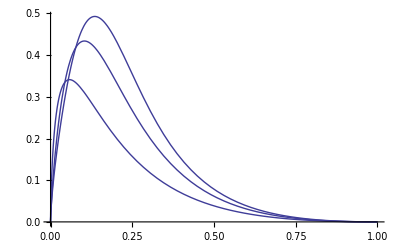

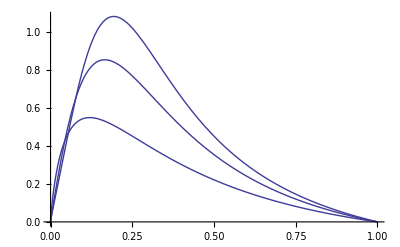

```mathematica
Z31=Plot[(64 μ (1+22 μ+157 μ^2+692 μ^3+1697 μ^4+3382 μ^5+4467 μ^6+3360 μ^7+1582 μ^8))/((-4/Log[μ])^2 *(1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2)*1/9,{μ,0,1}];
Z32=Plot[(64 μ (1+22 μ+157 μ^2+692 μ^3+1697 μ^4+3382 μ^5+4467 μ^6+3360 μ^7+1582 μ^8))/((-4/Log[μ])*(1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2)*1/9,{μ,0,1}];
Show[Z11,Z21,Z31,PlotRange->All]
Show[Z12,Z22,Z32,PlotRange->All]
```

Test for the susceptibility:

```mathematica
Clear[η,μ,T]
InitRGΩ
dηdH=-2η;
d2ηdH2=4η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0];
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0];
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
(Factor[(dηdH)^2*D[Log[Z[1]],{η,2}]/Z[1]]-(Factor[dηdH*D[Log[Z[1]],η]])^2)/.{η->1};
Simplify[Factor[dηdH^2*D[Log[Z[1]],{η,2}]+d2ηdH2*D[Log[Z[1]],{η,1}]]/.{η->1}]
Simplify[Factor[(term0+term1+term2+term3)]/.{η->1},Assumptions->{μ>0}]
Factor[(dηdH)^2*D[Log[Z[1]],{η,2}]/Z[1]]/.{η->1};
Simplify[Factor[D[Factor[dηdH*D[Log[Z[1]],η]],η]*dηdH]/.{η->1}]
```

(3 (3+μ))/(1+3 μ)

(3 (3+μ))/(1+3 μ)

(3 (3+μ))/(1+3 μ)

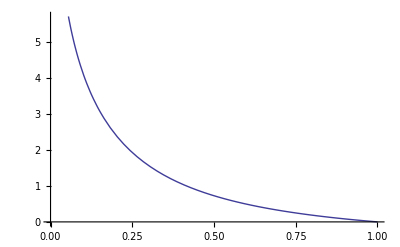

```mathematica
Plot[-(3 (3+μ))/(1+3 μ)/4*Log[μ],{μ,0,1}]
```

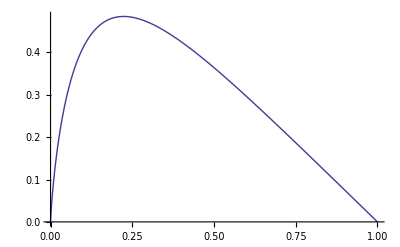

```mathematica
η=1;
Plot[(12 η (3 η^2+μ+4 η μ+4 η^3 μ+η^4 μ+3 η^2 μ^2))/((-4/Log[μ])(1+η)^2 (1-η+η^2+3 η μ)^2)*μ,{μ,0,1}]
Clear[η];
```

```mathematica
RGΩ;
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0];
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0];
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Factor[dηdH^2*D[Log[Z[2]],{η,2}]+d2ηdH2*D[Log[Z[2]],{η,1}]]
Factor[(term0+term1+term2+term3)/%]
```

0

1

```mathematica
RGΩ;
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0];
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0];
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Factor[dηdH^2*D[Log[Z[3]],{η,2}]+d2ηdH2*D[Log[Z[3]],{η,1}]]
Factor[(term0+term1+term2+term3)/%];
```

0

1

```mathematica
Clear[η,μ]
InitRGΩ
dμdβ=-4μ
d2μdβ2=16μ
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}]
d2A0dμ2=D[dA0dμ,μ]
η=1
μ=N[2/10,400]

For[iii=0,iii<30,iii++,
RGΩ;
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=(dμdβ)^2*(d2A0dμ2.Υ).DlnZ;
term1=d2μdβ2*(dA0dμ.Υ).DlnZ;
term2=dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ);
term3=dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ);
Print[iii,"   ",N[(term0+term1+term2+term3)/2^iii,20]];
]
```

-4 μ

16 μ

{0,0,1,1,0}

{0,0,0,0,0}

1

```mathematica
sh[T_,kmax_]:=Block[{k,DZ1,DZ2,term1,term2,term0,term3},
Clear[μ,η];
InitRGΩ;
μ=N[Exp[-2/T],400];
η=1;
For[k=1,k<kmax,k++,RGΩ];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=(dμdβ)^2*(d2A0dμ2.Υ).DlnZ;
term1=d2μdβ2*(dA0dμ.Υ).DlnZ;
term2=dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ);
term3=dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ);
Return[(term0+term1+term2+term3)/2^kmax];
]
```

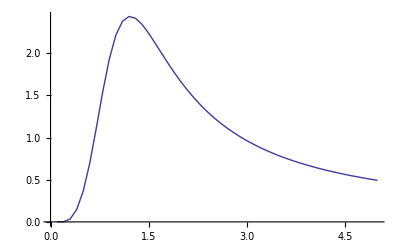

```mathematica
P1=ListPlot[Table[{t/10,10sh[t/10,3]/t},{t,1,50}],Joined->True]
```

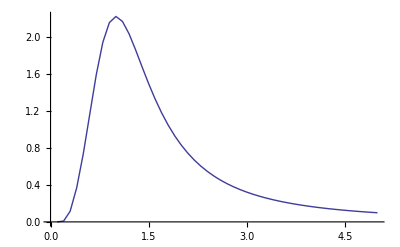

```mathematica
shE[k_]:=Block[{c},
Clear[η,μ];
c=Factor[(dμdβ^2*D[Log[Z[k]],{μ,2}]+d2μdβ2*D[Log[Z[k]],{μ,1}])/.η->1];
Return[c/2^k];
]
```

```mathematica
shE[3]
```

(8 μ (1+22 μ+157 μ^2+692 μ^3+1697 μ^4+3382 μ^5+4467 μ^6+3360 μ^7+1582 μ^8))/((1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2)

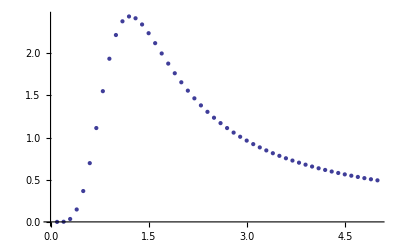

```mathematica
P2=ListPlot[Table[{t/10,10(%/.μ->Exp[-20/t])/t},{t,1,50}]]
```

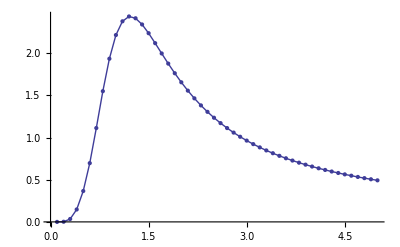

```mathematica
Show[P1,P2]
```

```mathematica
Chi[T_,kmax_]:=Block[{k,DZ1,DZ2,term1,term2,term0,term3},
Clear[μ,η];
InitRGΩ;
μ=N[Exp[-4/T],400];
η=1;
For[k=1,k<kmax,k++,RGΩ];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Return[(term0+term1+term2+term3)/2^kmax];
]
```

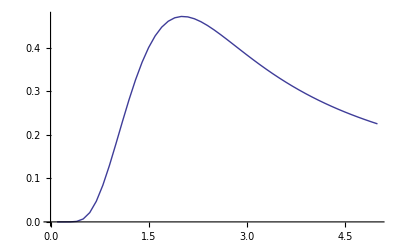

```mathematica
PX1=ListPlot[Table[{t/10,10/t*Exp[-40/t]*Chi[t/10,3]},{t,1,50}],Joined->True]
```

```mathematica
ChiE[k_]:=Block[{c},
Clear[η,μ];
c=Factor[(dηdH^2*D[Log[Z[k]],{η,2}]+d2ηdH2*D[Log[Z[k]],{η,1}])/.η->1];
Return[c/2^k];
]
```

```mathematica
ChiE[3]
```

(81+196 μ+534 μ^2+668 μ^3+673 μ^4+152 μ^5)/(8 (1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5))

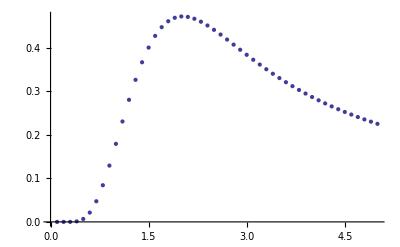

```mathematica
PX2=ListPlot[Table[{t/10,(10/t(μ*%)/.μ->Exp[-40/t])},{t,1,50}]]
```

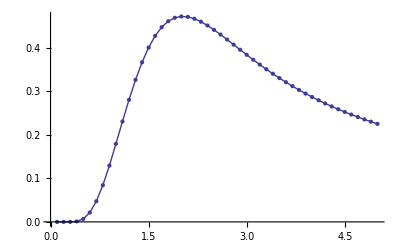

```mathematica
Show[PX1,PX2]
```

```mathematica
HierChi[T_,level_,kmax_]:=Block[{k,DZ1,DZ2,term1,term2,term0,term3},
Clear[μ,η];
InitRGΩ;
μ=N[Exp[-4/T],400];
η=1;
For[k=1,k<kmax,k++,If[k>level,RGΩ,RG]];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Return[(term0+term1+term2+term3)/2^(kmax-level)];
]
```

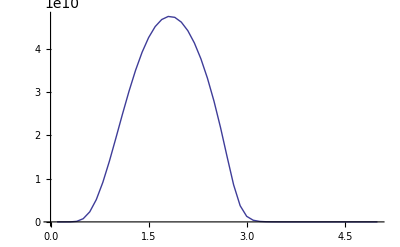

```mathematica
PX20=ListPlot[Table[{t/10,10/t*Exp[-40/t]HierChi[t/10,0,40]},{t,1,50}],Joined->True]
```

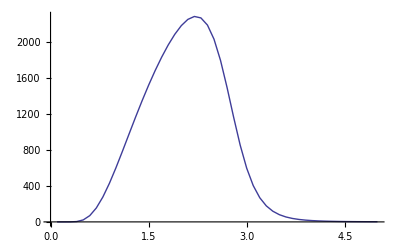

```mathematica
PX10=ListPlot[Table[{t/10,10/t*Exp[-40/t]HierChi[t/10,5,20]},{t,1,50}],Joined->True]
```

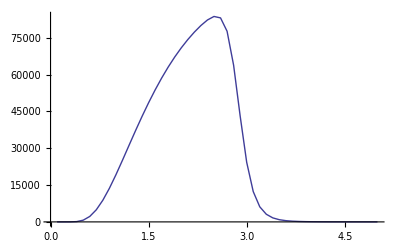

```mathematica
PX10=ListPlot[Table[{t/10,10/t*Exp[-40/t]HierChi[t/10,20,40]},{t,1,50}],Joined->True]
```

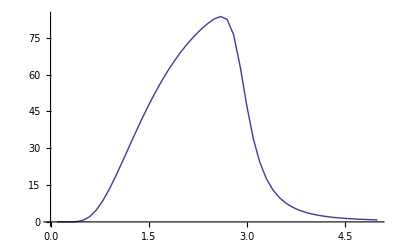

```mathematica
PX10=ListPlot[Table[{t/10,10/t*Exp[-40/t]HierChi[t/10,30,40]},{t,1,50}],Joined->True]
```

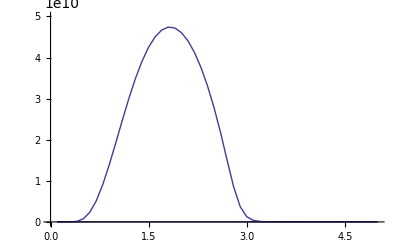

```mathematica
Show[PX10,PX20,PlotRange->{{0,5},{0,5*10^10}}]
```